## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsUNITmartinrimas(*LECsNUCLmartinrimas[[All,{1,2,3}]]*);
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1.;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[2]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_,l_]:=Module[{localcore=x,locall=l},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];
TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/Re[tanDp⟦All,2⟧]}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Transpose[{tanDs⟦All,1⟧, ArcTan[tanDs⟦All,2⟧]}];
phaseP=Transpose[{tanDp⟦All,1⟧, ArcTan[tanDp⟦All,2⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];
Print[Tfits];
Print[Tfitp];
GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]//Print
]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

λ=1.5  , core={{0.13337,0.864764},{0.00234178,0.0569715},{0.0715336,0.356374},{0.0213427,0.14449},{0.0780774,2.05587}}

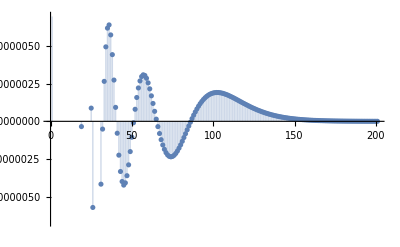

λ=2.  , core={{0.0720367,0.681458},{0.00558101,0.0743067},{0.0454778,0.223163},{0.072044,0.681449},{0.167546,2.09896}}

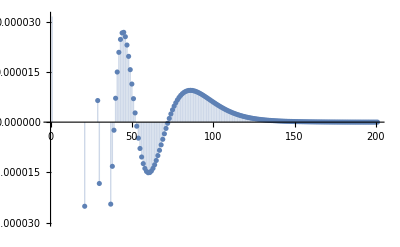

λ=3.  , core={{0.296093,2.09947},{0.0608917,0.463591},{0.00035901,1.28514},{0.0174451,0.114388},{0.0612714,0.463488}}

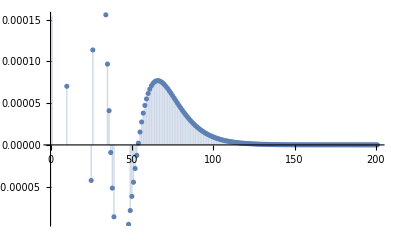

λ=4.  , core={{0.0344018,0.390968},{0.0344154,0.390968},{0.364441,2.09999},{0.0343997,0.390968},{0.0113235,0.0972307}}

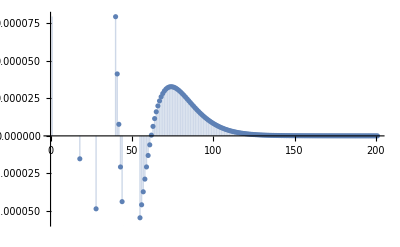

λ=6.  , core={{0.00605627,0.0769027},{0.0283325,0.320603},{0.0283325,0.320603},{0.435559,2.1},{0.0283325,0.320603}}

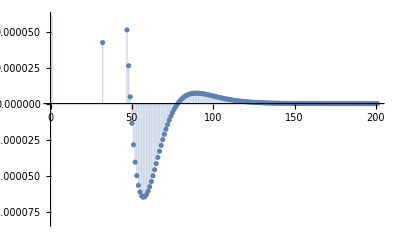

λ=8.  , core={{0.0000158732,2.01028},{0.0380443,0.28837},{0.00397155,0.0659773},{0.0380443,0.28837},{0.473718,2.1}}

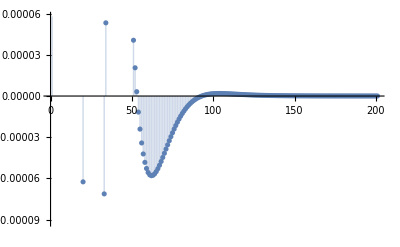

λ=10.  , core={{0.00291747,0.0597876},{0.0234263,0.269906},{0.500369,2.09983},{0.0234259,0.269906},{0.0234263,0.269906}}

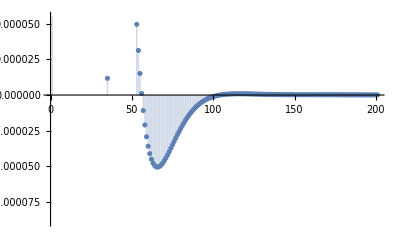

```mathematica
nk=5;

rmip=0.0;
rmap=21;

wfCores={};
wfs={};
w1=1;
amax=10^1;amin=0;
bmin=0.0;bmax=2.1;
w2=Min[Length[#]&/@Mϕ];
Do[
data=Mϕ[[ll]][[w1;;w2]];

modelGauss={Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-0.1,0.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel,Weights->((#+1)^3&/@data[[All,1]])];
nlresi=nlmLABC["FitResiduals"];
(*modelGauss=Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}];
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-10.1,10.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel];*)
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
AppendTo[wfCores,basispara];
AppendTo[wfs,Normal[nlmLABC]];

Print["λ=",wflambdas[[ll]],"  , core=",wfCores[[-1]]];
GraphicsGrid[{{
Show[ListLogLogPlot[Mϕ[[ll]],PlotLabel->"Λ = "<>ToString[wflambdas[[ll]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]<>"    Case: "<>ToString[sy]],
LogLogPlot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full, AxesLabel->{"r [fm]","WaveFunction"}],ImageSize->Scaled[.8]],ListPlot[nlresi,Filling->Axis],
Plot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->Scaled[.8]]
}},ImageSize->{{1200},{1700}}]//Print
,{ll,Range[Length[wflambdas]]}];
```

## The real pudding

nn=1  nwf=1  λ=0.5625  C0=-62.6076  D0=-13.365  core={{0.13337,0.864764},{0.00234178,0.0569715},{0.0715336,0.356374},{0.0213427,0.14449},{0.0780774,2.05587}}

S Pole Poitions in momentum: {-1.15461-0.405743 ⅈ,-0.120748+0.405743 ⅈ,0.120748+0.405743 ⅈ,1.15461-0.405743 ⅈ}

S Pole Poitions in energy:   {32.306+25.9043 ⅈ,-4.14842-2.70904 ⅈ,-4.14842+2.70904 ⅈ,32.306-25.9043 ⅈ}

P Pole Poitions in momentum: {-0.16813-0.346253 ⅈ,-0.0740836+0.414656 ⅈ,0.0740836+0.414656 ⅈ,0.16813-0.346253 ⅈ}

P Pole Poitions in energy:   {-2.53315+3.21901 ⅈ,-4.60194-1.69861 ⅈ,-4.60194+1.69861 ⅈ,-2.53315-3.21901 ⅈ}

-0.250854+0.951839 p^2-0.934591 p^4

0.192153+1.81803 p^2+7.30963 p^4

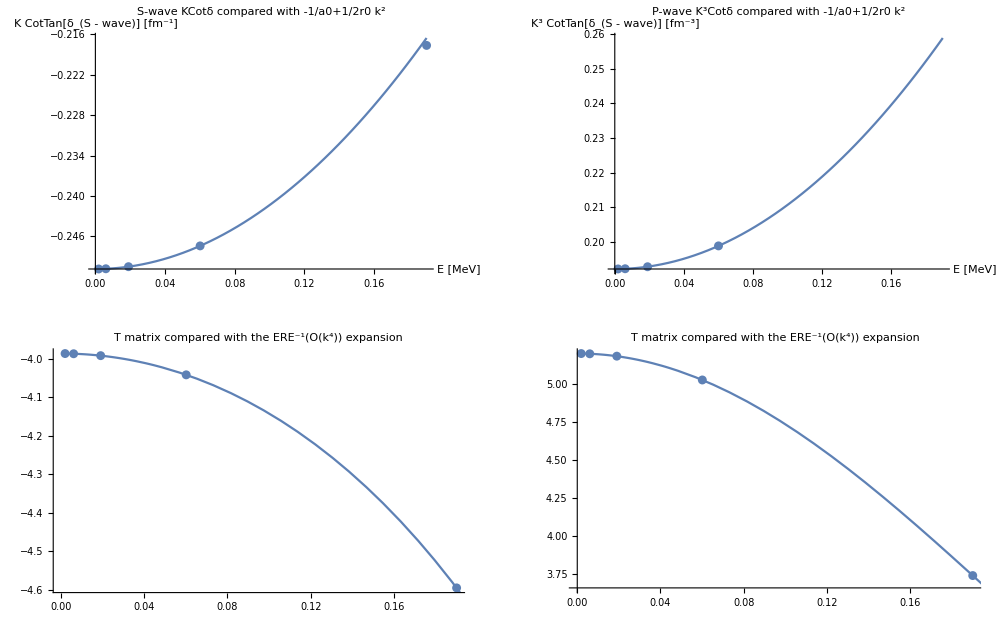

λ = Λ^2/4 = 0.5625 ; R_max = 21.3000:   a0 = 3.98639     r0 = 1.89673     a1 = -5.20428     r1 = 3.69044

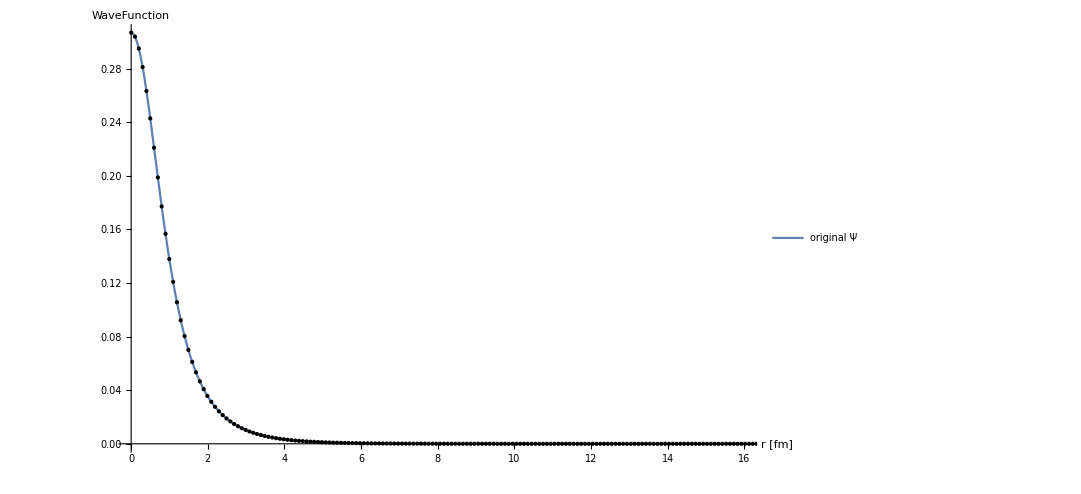

nn=2  nwf=2  λ=1.  C0=-111.302  D0=8.462  core={{0.0720367,0.681458},{0.00558101,0.0743067},{0.0454778,0.223163},{0.072044,0.681449},{0.167546,2.09896}}

S Pole Poitions in momentum: {-1.08037-0.417611 ⅈ,-0.133756+0.417611 ⅈ,0.133756+0.417611 ⅈ,1.08037-0.417611 ⅈ}

S Pole Poitions in energy:   {27.4484+24.9476 ⅈ,-4.32705-3.08866 ⅈ,-4.32705+3.08866 ⅈ,27.4484-24.9476 ⅈ}

P Pole Poitions in momentum: {-0.185326-0.335818 ⅈ,-0.143933+0.384166 ⅈ,0.143933+0.384166 ⅈ,0.185326-0.335818 ⅈ}

P Pole Poitions in energy:   {-2.16832+3.4413 ⅈ,-3.50752-3.05748 ⅈ,-3.50752+3.05748 ⅈ,-2.16832-3.4413 ⅈ}

-0.268745+0.871203 p^2-1.04174 p^4

0.256062+2.07474 p^2+10.3417 p^4

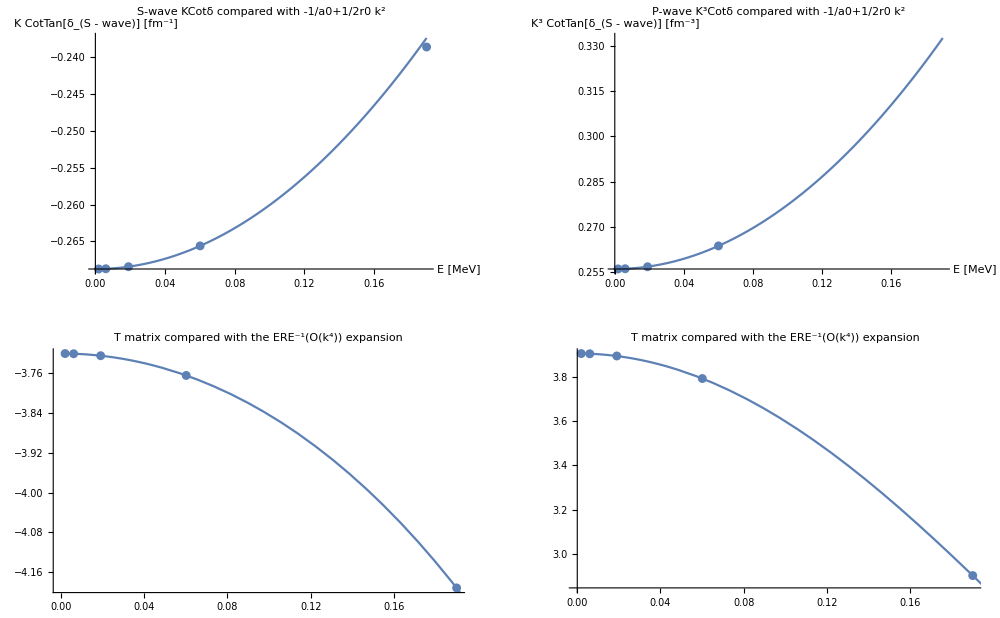

λ = Λ^2/4 = 1.0000 ; R_max = 21.3000:   a0 = 3.72101     r0 = 1.73467     a1 = -3.90538     r1 = 4.22644

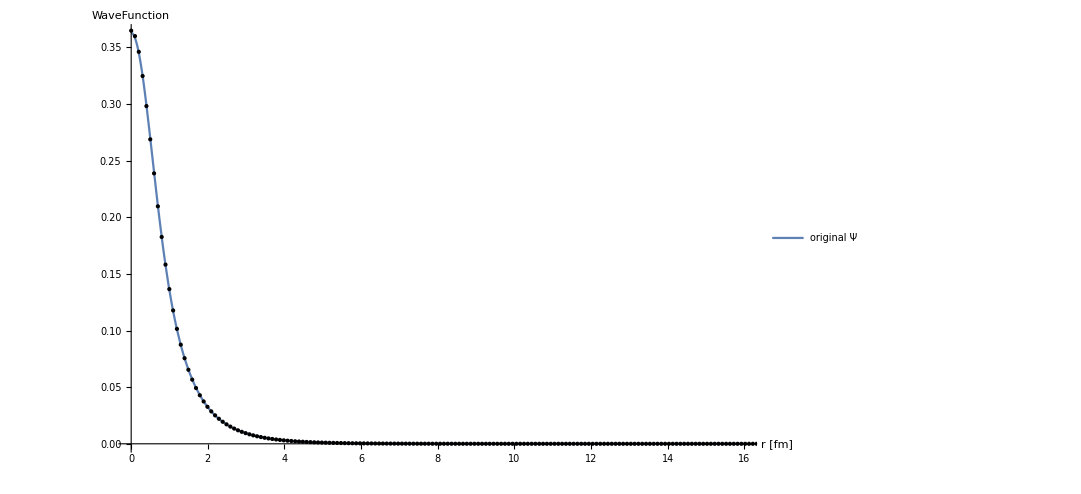

nn=3  nwf=3  λ=2.25  C0=-250.43  D0=123.178  core={{0.296093,2.09947},{0.0608917,0.463591},{0.00035901,1.28514},{0.0174451,0.114388},{0.0612714,0.463488}}

S Pole Poitions in momentum: {-1.14479-0.459944 ⅈ,-0.158162+0.459944 ⅈ,0.158162+0.459944 ⅈ,1.14479-0.459944 ⅈ}

S Pole Poitions in energy:   {30.3844+29.1149 ⅈ,-5.15716-4.02244 ⅈ,-5.15716+4.02244 ⅈ,30.3844-29.1149 ⅈ}

P Pole Poitions in momentum: {-0.211559-0.309275 ⅈ,-0.200126+0.334127 ⅈ,0.200126+0.334127 ⅈ,0.211559-0.309275 ⅈ}

P Pole Poitions in energy:   {-1.40708+3.61793 ⅈ,-1.97928-3.69741 ⅈ,-1.97928+3.69741 ⅈ,-1.40708-3.61793 ⅈ}

-0.304489+0.771611 p^2-0.845632 p^4

0.428523+2.43949 p^2+20.1197 p^4

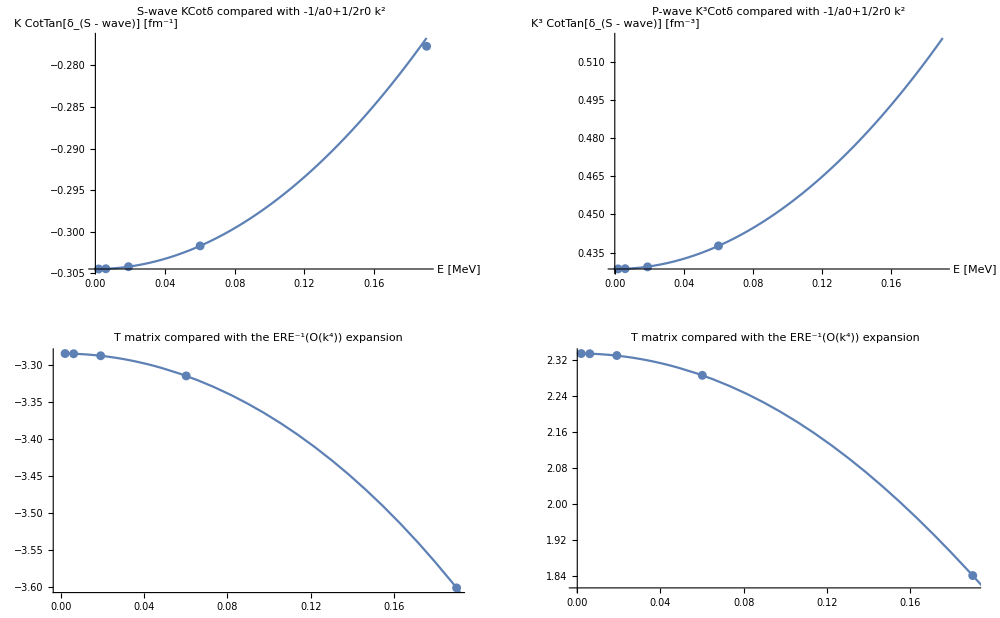

λ = Λ^2/4 = 2.2500 ; R_max = 21.3000:   a0 = 3.28419     r0 = 1.53694     a1 = -2.33365     r1 = 5.02883

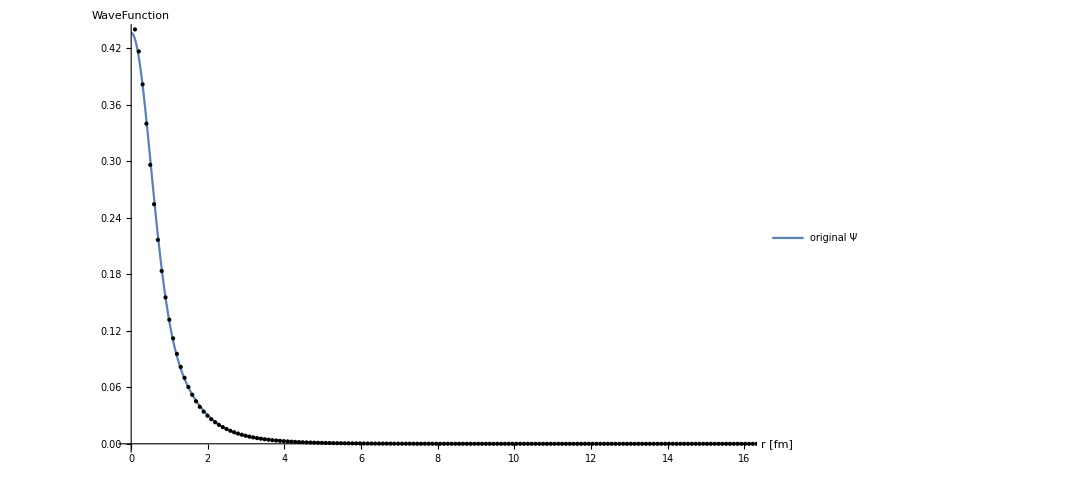

nn=4  nwf=4  λ=4.  C0=-445.21  D0=372.602  core={{0.0344018,0.390968},{0.0344154,0.390968},{0.364441,2.09999},{0.0343997,0.390968},{0.0113235,0.0972307}}

S Pole Poitions in momentum: {-0.997612-0.441421 ⅈ,-0.147954+0.441421 ⅈ,0.147954+0.441421 ⅈ,0.997612-0.441421 ⅈ}

S Pole Poitions in energy:   {22.1283+24.3499 ⅈ,-4.78194-3.6113 ⅈ,-4.78194+3.6113 ⅈ,22.1283-24.3499 ⅈ}

P Pole Poitions in momentum: {-0.199237-0.305674 ⅈ,-0.187845+0.327936 ⅈ,0.187845+0.327936 ⅈ,0.199237-0.305674 ⅈ}

P Pole Poitions in energy:   {-1.48581+3.36754 ⅈ,-1.99769-3.40622 ⅈ,-1.99769+3.40622 ⅈ,-1.48581-3.36754 ⅈ}

-0.300175+0.730144 p^2-1.16373 p^4

0.427078+2.80766 p^2+22.4601 p^4

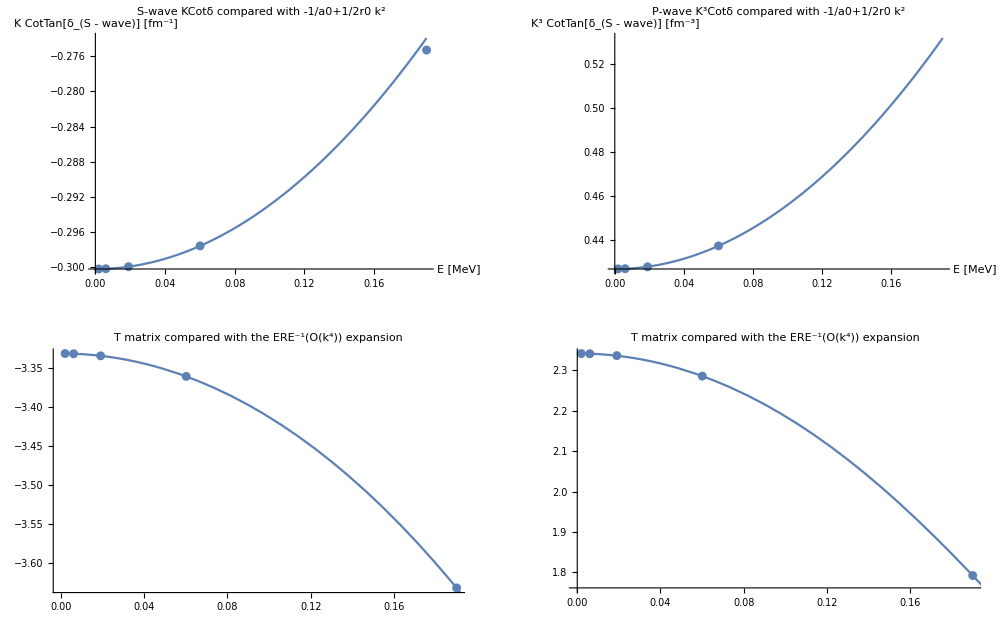

λ = Λ^2/4 = 4.0000 ; R_max = 21.3000:   a0 = 3.3314     r0 = 1.45164     a1 = -2.34154     r1 = 5.78255

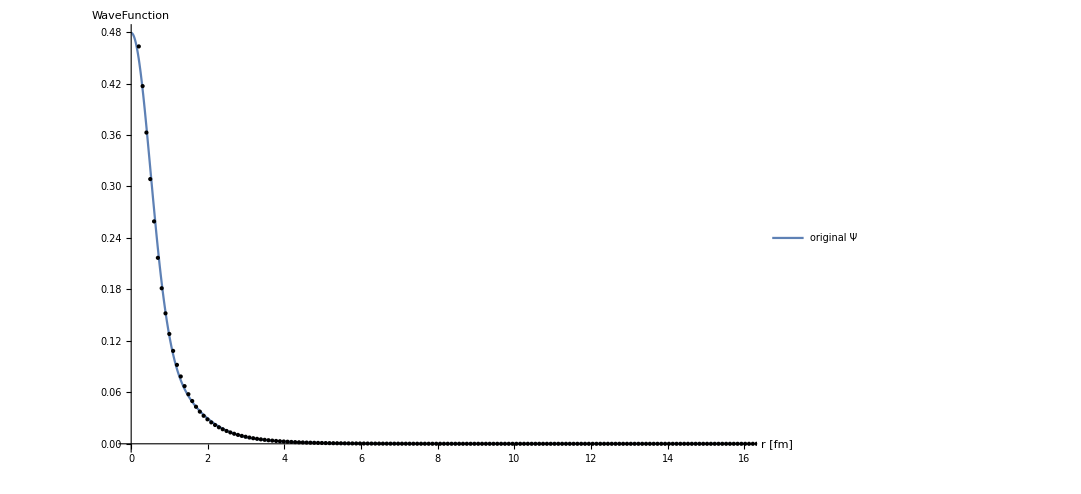

nn=5  nwf=5  λ=9.  C0=-1001.72  D0=1524.25  core={{0.00605627,0.0769027},{0.0283325,0.320603},{0.0283325,0.320603},{0.435559,2.1},{0.0283325,0.320603}}

S Pole Poitions in momentum: {-0.845932-0.417963 ⅈ,-0.133674+0.417963 ⅈ,0.133674+0.417963 ⅈ,0.845932-0.417963 ⅈ}

S Pole Poitions in energy:   {14.9547+19.5504 ⅈ,-4.33577-3.08935 ⅈ,-4.33577+3.08935 ⅈ,14.9547-19.5504 ⅈ}

P Pole Poitions in momentum: {-0.180649-0.298794 ⅈ,-0.169242+0.317918 ⅈ,0.169242+0.317918 ⅈ,0.180649-0.298794 ⅈ}

P Pole Poitions in energy:   {-1.56605+2.98463 ⅈ,-2.00248-2.97514 ⅈ,-2.00248+2.97514 ⅈ,-1.56605-2.98463 ⅈ}

-0.293932+0.658521 p^2-1.71453 p^4

0.413446+3.35545 p^2+26.1447 p^4

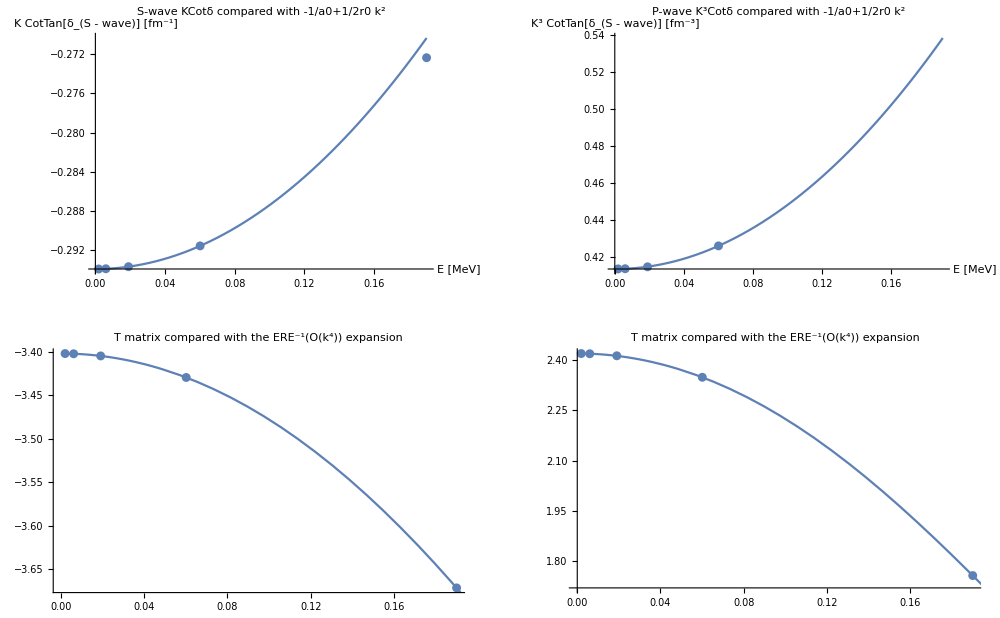

λ = Λ^2/4 = 9.0000 ; R_max = 21.3000:   a0 = 3.40216     r0 = 1.3043     a1 = -2.41876     r1 = 6.90547

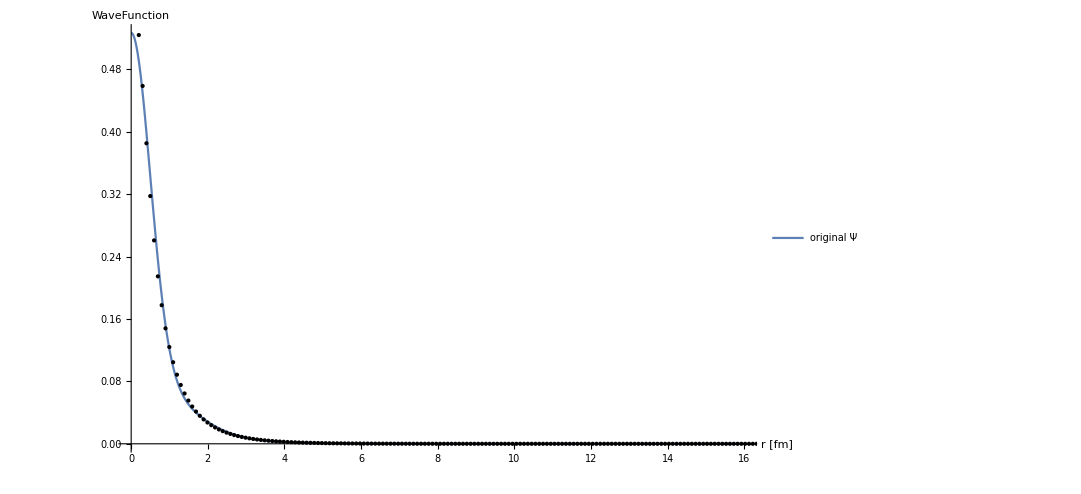

nn=6  nwf=6  λ=16.  C0=-1780.84  D0=4165.55  core={{0.0000158732,2.01028},{0.0380443,0.28837},{0.00397155,0.0659773},{0.0380443,0.28837},{0.473718,2.1}}

S Pole Poitions in momentum: {-0.76401-0.405472 ⅈ,-0.12411+0.405472 ⅈ,0.12411+0.405472 ⅈ,0.76401-0.405472 ⅈ}

S Pole Poitions in energy:   {11.5926+17.1294 ⅈ,-4.11958-2.78259 ⅈ,-4.11958+2.78259 ⅈ,11.5926-17.1294 ⅈ}

P Pole Poitions in momentum: {-0.168526-0.291717 ⅈ,-0.157662+0.308501 ⅈ,0.157662+0.308501 ⅈ,0.168526-0.291717 ⅈ}

P Pole Poitions in energy:   {-1.56753+2.71839 ⅈ,-1.94405-2.68947 ⅈ,-1.94405+2.68947 ⅈ,-1.56753-2.71839 ⅈ}

-0.291885+0.586503 p^2-2.16983 p^4

0.405827+3.76681 p^2+29.789 p^4

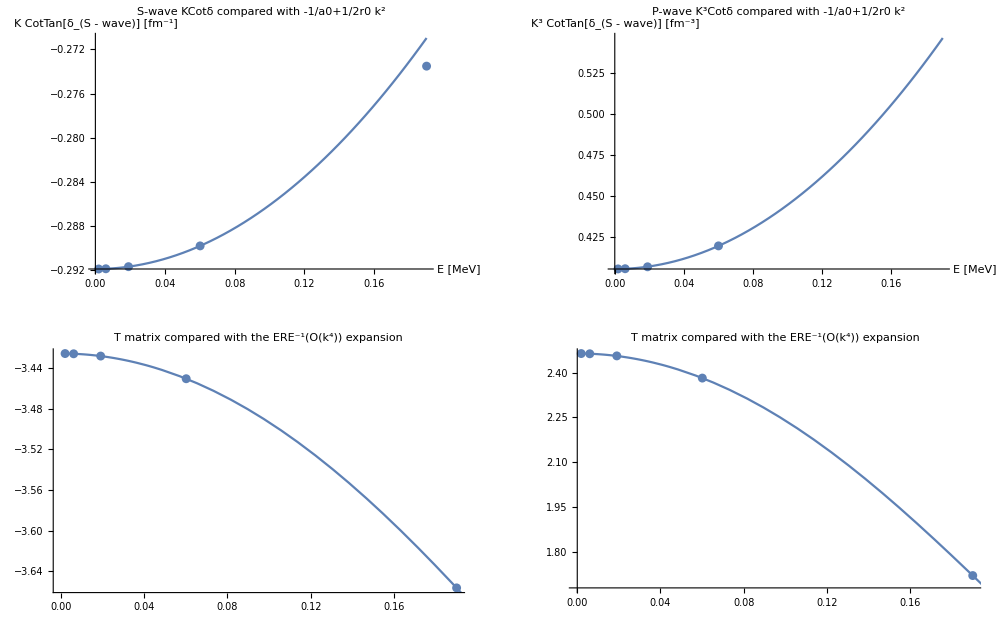

λ = Λ^2/4 = 16.0000 ; R_max = 21.3000:   a0 = 3.42602     r0 = 1.15688     a1 = -2.46418     r1 = 7.75524

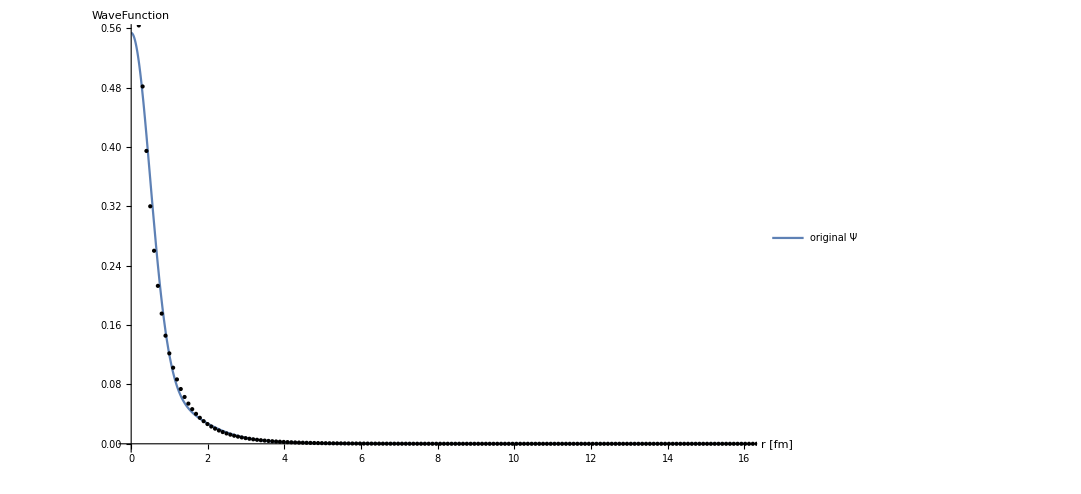

nn=7  nwf=7  λ=25.  C0=-2782.56  D0=9491.9  core={{0.00291747,0.0597876},{0.0234263,0.269906},{0.500369,2.09983},{0.0234259,0.269906},{0.0234263,0.269906}}

S Pole Poitions in momentum: {-0.714118-0.401798 ⅈ,-0.1173+0.401798 ⅈ,0.1173+0.401798 ⅈ,0.714118-0.401798 ⅈ}

S Pole Poitions in energy:   {9.63571+15.8658 ⅈ,-4.08303-2.60609 ⅈ,-4.08303+2.60609 ⅈ,9.63571-15.8658 ⅈ}

P Pole Poitions in momentum: {-0.161656-0.284966 ⅈ,-0.151994+0.299546 ⅈ,0.151994+0.299546 ⅈ,0.161656-0.284966 ⅈ}

P Pole Poitions in energy:   {-1.52262+2.54722 ⅈ,-1.84202-2.51752 ⅈ,-1.84202+2.51752 ⅈ,-1.52262-2.54722 ⅈ}

-0.295001+0.503676 p^2-2.50785 p^4

0.415321+4.15883 p^2+34.293 p^4

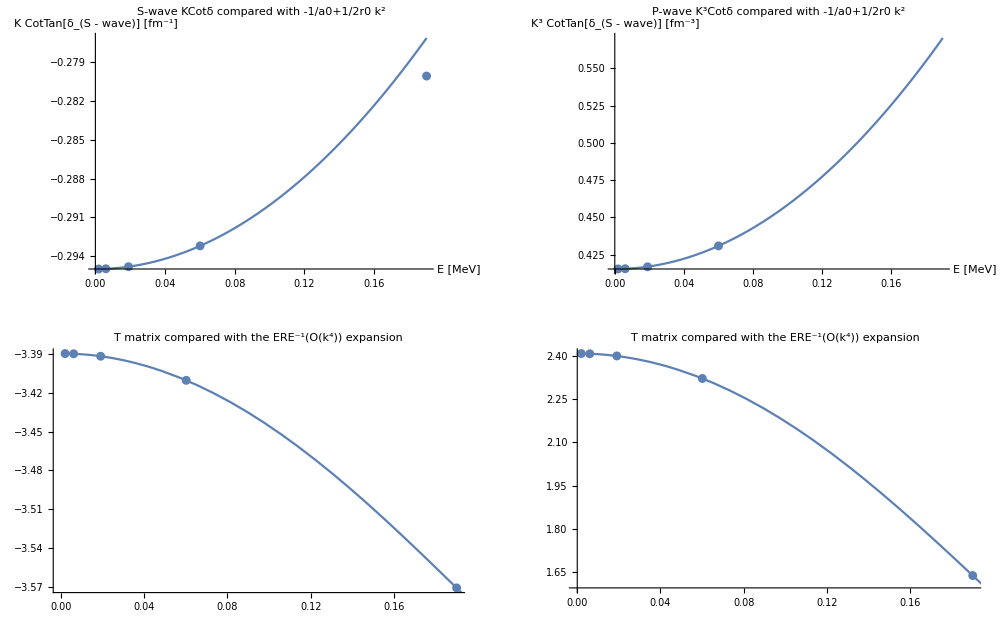

λ = Λ^2/4 = 25.0000 ; R_max = 21.3000:   a0 = 3.38984     r0 = 0.988718     a1 = -2.40786     r1 = 8.57276

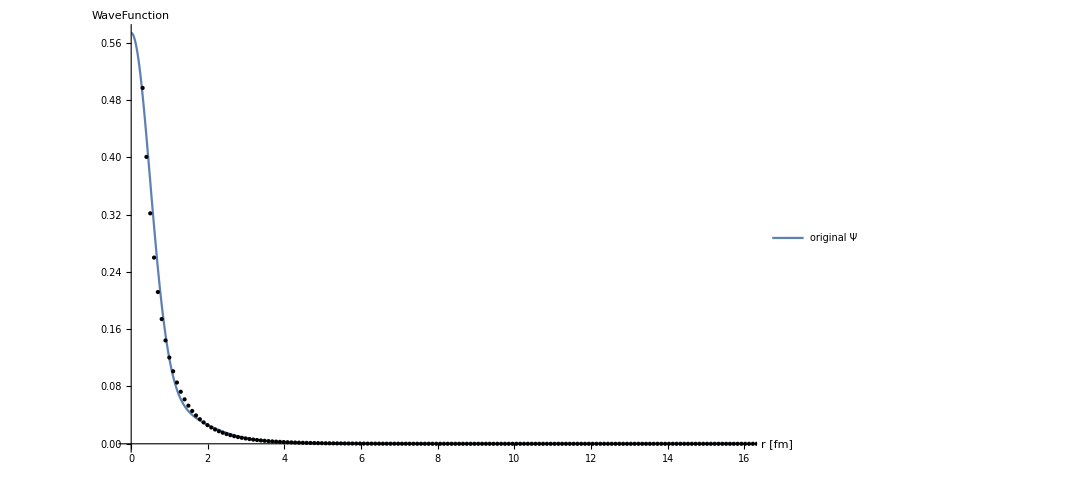

```mathematica
rGrid= {21.3}(*Subdivide[6.5,22.1,2]*); 
rr=rGrid[[1]];
EREs={};
lRange=Range[1,Length[wflambdas]];

nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.002;
k0FMax=0.1;
Divisions=6;
rmip=0.0;
rmap=16;
(*---------------------*)
ErangeMeV=N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];
Erange1onfm=Sqrt[mh2 ErangeMeV];
exportdata={};
Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[ll]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[ll]];
Print["nn=",nn,"  nwf=",ll,"  λ=",λ,"  C0=",C0,"  D0=",D0,"  core=",mycore];
ERE=GetERE[mycore,λ];
PlotERE;
AppendTo[EREs,ERE];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧];
tmpwfs=Total[#⟦1⟧ⅇ^(-#⟦2⟧ r^2)&/@mycore];
Plot[tmpwfs,{r,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->800]//Print;
AppendTo[exportdata,Join[{λ,nGrid,rr},ERE[[;;4]],Polesp,PolesE,Polepp,PolepE,Flatten[mycore]]];
,{ll,lRange}];
,{rr,rGrid}];
Export["/tmp/tmp.dat",exportdata,"Table"];
```

```mathematica
model=a+b/x+c/x^2;
l0=2;
lambdas=exportdata[[All,1]];
a0s=Transpose[{lambdas,exportdata[[All,4]]}];
fita0=model/.FindFit[a0s[[l0;;]],model,{a,b,c},x];
r0s=Transpose[{wflambdas,exportdata[[All,5]]}];
fitr0=model/.FindFit[r0s[[l0;;]],model,{a,b,c},x];
a1s=Transpose[{wflambdas,exportdata[[All,6]]}];
fita1=model/.FindFit[a1s[[l0;;]],model,{a,b,c},x];
r1s=Transpose[{wflambdas,exportdata[[All,7]]}];
fitr1=model/.FindFit[r1s[[l0;;]],model,{a,b,c},x];
legs="R_max="<>ToString[rr];
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,lambdas[[-1]]},ImageSize->Large]]
}}]
```

-Graphics-

```mathematica
ComplexPlot
```

```mathematica
cplxpoleSp=Transpose[{Re[exportdata[[All,8+#]]],Im[exportdata[[All,8+#]]]}]&/@{0,1,2,3};
cplxpolePp=Transpose[{Re[exportdata[[All,16+#]]],Im[exportdata[[All,16+#]]]}]&/@{0,1,2,3};
GraphicsGrid[{{
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpoleSp]
,
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpolePp]
}}
]
```

-Graphics-

```mathematica
nwf=7;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]]
rprime=2.1;sca=1.;rMax=6;
eplot=ErangeMeV[[1]];
(*Plot[{WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],0,mh2],WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},PlotRange->Full,PlotLegends->{"L_rel=0","L_rel=1"}]*)

GraphicsGrid[{{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]},{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]
}},ImageSize->Full]
λ
C0
D0
```

{{0.258496,1.45748},{0.0859085,0.218432}}

-Graphics-

25.

-2929.17

92495.